# Introduction to Mathematica

## Based on: Labs by John S. Colton, BYU Physics & Astronomy, based on previous labs by Branton Cambell and Steve Turley. Source: BYU Physics 230 This is the first of a series of Mathematica labs you can find on the BYU Physics 230 website, with some modifications to better suit our course Phys-300. For more help in learning Mathematica the other labs on the BYU website are a great resource.

Mathematica is a cross between a souped-up calculator and a full-blown programming language. You will mostly be typing and entering commands. 

To enter a command: Move the pointer/cursor to a spot between two “cells” (the smallest unit grouped by the brackets on the right), identifiable because the mouse cursor turns into a horizontal indicator, click, and type what you want Mathematica to do. Then press “shift-enter” (or just “enter” if you use the enter key on the numeric keypad) to have your command executed. Regular “enter” will not work--that’s for adding line breaks inside a command, for example if you want to run two commands at the same time.  If “shift-enter” doesn’t execute the command, then select the new cell (click on the vertical bracket on the right), then choose menu option Format→Style→Input and try again.

Probably the most helpful piece of advice in using Mathematica: If you are typing Mathematica commands and things are not working the way you expect, go to Evaluation→Quit Kernel→Local. That clears the memory and will restart the Mathematica engine the next time you enter a command. Just as the way to solve most computer problems is to turn it off and on again, the way to solve most Mathematica problems is to turn off the kernel (the processing engine) and then turn it on again. Evaluation→Abort can also be quite useful, to stop the execution of the current command if things are taking much longer than expected. 

To expand/contract the selections below: Double-click the vertical bars on the right that look like they have half of a downward-pointing arrow. To contract them, double-click the same bar (now potentially quite long). Or, go to  Edit→Preferences→Interface  and check the box that says “Show open/close icons for cell groups” (it may already be checked). That will give you carat-shaped icons on the left which will toggle the sections between expanded and contracted.

To expand/contract all groups at once: Here are two potentially useful shortcuts. To expand all groups at once, type Control-A (to select everything in the notebook), then choose the menu option Cell→Grouping→Open all subgroups. Similarly, to contract all groups, type Control-A then use menu option Cell→Grouping→Close all subgroups. Or, to close some but not all of the groups, just select the ones you want to close instead of using Control-A.

To delete cells or groups: Click or click-drag on the vertical bar on the right to select the cell, cells, or groups you wish to delete.  Press Del on the keypad.

## *The Most Useful Commands

### How to use Mathematica as a calculator

Calculator commands: Basic calculator-like commands such as +, -, *, /, and ^ all work pretty much like you’d expect. Regular parentheses can be used to group terms. Click on each of the equations below, and then press shift-enter to run these commands. When you do so, the equations will become labeled as input lines and output lines with the solution will appear. To experiment on your own, feel free to edit an equation on an input line and press shift-enter again. Or start typing in between cells, as mentioned above, to create your own input. Note, a “Suggestion Bar” will appear the first time that you execute a command. It can be closed with the “x” icon on the right.

```mathematica
1+1
```

2

```mathematica
4-5
```

-1

```mathematica
6*5
```

30

```mathematica
6^5
```

7776

```mathematica
1+(2-3)/5
```

4/5

Scientific notation can be indicated two ways. In the second method, there is no space between the number and the * character.

```mathematica
6.022 * 10^23
```

6.022×10^23

```mathematica
6.022*^23
```

6.022×10^23

You can either specify “times” by the * character, or more simply by leaving a space between two numbers. Mathematica will add the x character automatically. That’s what I did here:

```mathematica
6 5
7 9
```

30

63

Tip: Shift-enter(keypad) not only executes the command like shift-enter and enter(keypad) do, it also positions the cursor at the next available input field. You may find that to be a helpful shortcut when evaluating a series of commands in a row.

Another Tip: Your cursor can be anywhere in the input box when you press Enter or Shift-Enter to execute the command - it does NOT have to be at the end of the command line.

Yet Another Tip: To evaluate all of the commands in a notebook, use Control-A to select all, then shift-enter. I wouldn’t necessarily advise doing that here, but it will be very useful in your own notebooks.

One more: Notice that you can stack several input lines on top of one another, as in the last example above.  Just press Enter to start the next line.

Built-in Functions: Giving Mathematica a function as a command is termed “calling the function”, or issuing a “function call”. The parameters that you use when calling the function are called the “arguments”. There are a ton of built-in functions. For example:

```mathematica
Log[1]
```

0

```mathematica
Log10[100]
```

2

```mathematica
Sqrt[10]
```

√10

```mathematica
N[%]
```

3.16228

```mathematica
N[Sqrt[10],50]
```

3.1622776601683793319988935444327185337195551393252

```mathematica
Cos[1]
```

Cos[1]

```mathematica
N[%]
```

0.540302

Things to observe:

1. Function calls such as Log and Sqrt must use square brackets. 

2. Pre-defined functions such as Log and Sqrt must be capitalized. 

3. The “%” symbol gets interpreted as “the result of the previously- executed command”. %% means “the result of two commands ago” (and so on as you add more % signs). % followed by a number means “the result of line <number>”

4. The “N” command can be used to force a numerical decimal result. I use N[%] all the time when a command doesn’t give me a numerical result like I wanted.

5. Commas are used to separate additional arguments (parameters) for functions. The second argument to the N command, if used, specifies the number of significant figures you want Mathematica to supply.

6.  Trigonometric functions must use radians. The trig functions include Sin, Cos, Tan, ArcSin, ArcCos, ArcTan, and the equivalent hyperbolic trig functions Sinh, etc.

The second most helpful piece of advice you’ll get in using Mathematica:  Mathematica has many built-in functions, and outstanding online help. To find out more information about any function, click on the function name and press F1. Try that with some of the built-in functions above. You can also access help topics organized by category, and/or search for a particular topic by going to Help→Documentation Center. One cool feature is that you can actually edit examples inside the help documents and execute them with shift-enter.

Variables: You can assign names to store your results into the computer's memory as "variables".

```mathematica
a = 15
```

15

```mathematica
b = 2
```

2

```mathematica
a b
```

30

```mathematica
b = 35
```

35

```mathematica
a b
```

525

```mathematica
a^b
```

145610960604971353313885629177093505859375

```mathematica
c = a-b
```

-20

```mathematica
c
```

-20

```mathematica
b1 = 42
```

42

```mathematica
thisNumber=999999999
```

999999999

```mathematica
y+z
```

y+z

```mathematica
y+z * thisNumber
```

y+999999999 z

Things to observe:

1. You can give the variables any name you want (with a few exceptions), then you can refer to them by that name later.

2. You can use numbers in the variable name, like “b1” above, but you can’t start the name with a number.

3. You can have capital letters in the name of a variable, but it’s best not to start the name with a capital letter since that’s the way all of Mathematica’s built-in functions start.

4. If you try to use variables that have not been defined as anything, Mathematica will leave the answer as a symbolic expression. You can use this to do algebra, for example. More on that later.

Built-in Constants: Some variable names are reserved, such as Pi, E, I, and Infinity:

```mathematica
Sin[Pi/2]
```

1

```mathematica
N[E,50]
```

2.7182818284590452353602874713526624977572470937

```mathematica
(2 + 3 I) / (4 - 7 I)
```

-1/5+(2 ⅈ)/5

```mathematica
2^(-Infinity)
```

0

```mathematica
E = 10
```

Set::wrsym: Symbol ⅇ is Protected.

10

Things to observe:

1. Mathematica treats Pi and E just as you’d expect, as if you had defined them yourself to hundreds of decimal places.

2. A capital I is used to indicate complex numbers.

3. Infinity is kind of a strange constant, but it also works like you’d expect.

4. You cannot set the value of the built-in constants yourself. That’s why the last command gave an error messaage “Symbol e is protected”. This tends to be a problem with the letters “E” and “I” which are very tempting to use to stand for energy, electric field, or current. Remember when defining your own constants it’s best to start them with a lower case letter. That will prevent this problem with e or i.

Now try it out on your own: move the mouse directly below this paragraph (it's a break between cells) and when the mouse pointer turns into a horizontal bar, click to position the cursor there, and start typing. Calculate something that you might use a regular calculator for.

```mathematica
E^(I*Pi)
```

-1

↑

Enter your command above the arrow. (Notice the break between cells is indicated on the right.) Remember if “shift-enter” doesn’t execute the command, then select the new cell (click on the vertical bracket on the right), then choose menu option Format→Style→Input and try again. That won’t generally be an issue when you create your own new notebooks, but it may be here.

Now open up a brand-new notebook file using File→New→Notebook (or Control-N) and type in some  commands there. The formatting won’t look as cool as this notebook, but we’ll cover formatting later.

CAUTION:  Mathematica "remembers" variable assignments between notebooks. That is, if you've defined a=15 in this notebook, when you open a new notebook, it will equal 15 there, too! This can often cause unintended (and undesired) consequences. The "quit kernel" tip from the top of this notebook can be especially helpful under those circumstances.

### An aside: how to leave comments

The commands you’ve seen so far have been very simple and intuitive. That will change. In a complicated sequence of commands it's critically important to leave comments for yourself (and others), so that you (and they) will know what was going on in your head when you wrote the code that way. You do that in Mathematica via paired parentheses/asterisks:

```mathematica
hbar = 1.055*^-34   (* this is Plank's constant, divided by 2 Pi *)
```

1.055×10^-34

There’s a nice shortcut for toggling comments on and off: select the text you want to comment, then type Alt-?. Try that, here:

```mathematica
(*comment this out with Alt-?*)
```

#### Assignment 0: Basic computation

In a newly created cell below this assignment, do these computations. It might be good to check your answer against your calculator.
(a)  √(1+(2/(3-log_10 4)))  (give the answer to 10 sig figs)
(b) the answer to (a) + ln(2.39).

```mathematica
N[Sqrt[1+(2/(3-Log10[4]))],10]
%+Log[2.39]

Log[2.39]
```

1.354270735

2.22556

0.871293

### How to define a function

You can define your own functions, such as:

```mathematica
f[x_] = - x^4 + 3 x^3 +  4 Sin[x]
```

3 x^3-x^4+4 Sin[x]

```mathematica
f[2]
```

8+4 Sin[2]

```mathematica
N[%,30]
```

11.6371897073027267815840794636

```mathematica
f[a]
```

-40500+4 Sin[15]

```mathematica
N[%]
```

-40497.4

```mathematica
f[y]
```

3 y^3-y^4+4 Sin[y]

```mathematica
f[x^2]
```

3 x^6-x^8+4 Sin[x^2]

Things to observe:

1. Function definitions must use the underscore symbol after the variable (and square brackets!). Function calls do not use the underscore symbol.

2. You can evaluate your new function at a particular number such as 2 just the same way you would use a built-in function.

3. You can evaluate your function at a particular variable, or even at a function of a variable. In the examples above f[y] doesn’t get evaluated at a particular number because y is undefined. It just gets evaluated at the unknown variable “y”. And just as Sin[x^2] will compute sin of (x^2), f[x^2] will compute f of (x^2).

### How to plot a function

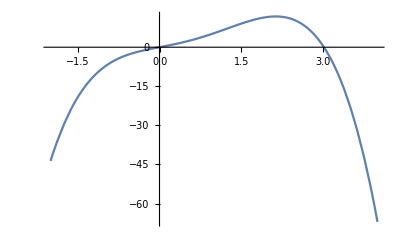

```mathematica
Plot[f[x],{x,-2,4}]
```

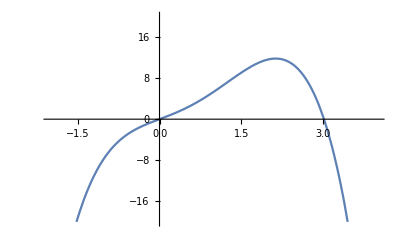

```mathematica
Plot[f[x],{x,-2,4}, PlotRange->{-20,20}]
```

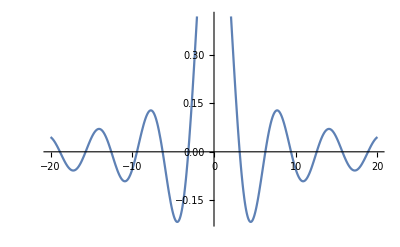

```mathematica
Plot[Sin[x]/x,{x,-20,20}]
```

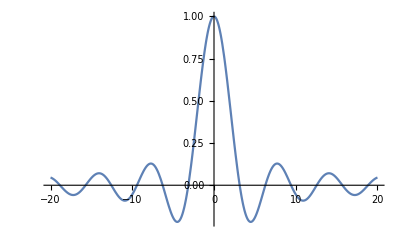

```mathematica
Plot[Sin[x]/x,{x,-20,20}, PlotRange->All]
```

Things to observe: 

1. Commands such as plot are treated in much the same way as functions such as sin or cos. In fact, I’ll likely often call them functions. In particular, like all other commands/functions, “plot” must be capitalized. 

2. Again, all commands/functions must be called with square brackets. 

3. When a function argument contain multiple values rather than a single number, it is typically done via curly braces. In this case, the second argument of the plot command, “{x,-2,4}” specifies the variable to be plotted, the start of the plot range, and the end of the plot range. 

4. The right arrow is often used to specify function parameters. It is produced automatically when you type “-” followed by “>”.
 
5. There are various settings you can give to the Plot command via additional arguments; PlotRange is probably the most useful of them. It specifies the vertical range for occasions when the automatic vertical scale doesn’t give you the range you want to see. The two most common ways to do it are to specify the range yourself with PlotRange->{low,high}, or to force Mathematica to display all y-values using PlotRange->All.

The third most helpful piece of advice you will get in using Mathematica: Be very VERY careful when choosing between parentheses (always used for arithmetic grouping), square brackets (always used in function calls/definitions), and braces (always used for lists of items). Mathematica is EXTREMELY picky about which is which, and will give you errors if you use them incorrectly. That's both good and bad--bad, because new users can easily get frustrated, but good, because once you get a little more experience the standardized notation protects you against doing things wrong accidentally.

Plotting two functions: You can plot two functions like this:

```mathematica
f1[x_]=Sin[x]
```

Sin[x]

```mathematica
f2[x_]=Cos[x]
```

Cos[x]

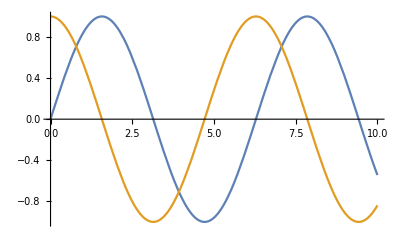

```mathematica
Plot[{f1[x],f2[x]},{x,0,10}]
```

or like this :



```mathematica
plot1=Plot[f1[x],{x,0,10}]
```

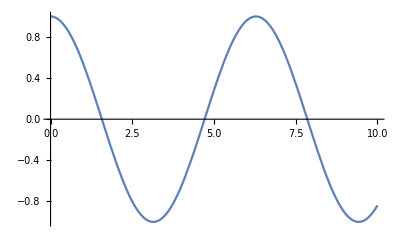

```mathematica
plot2=Plot[f2[x],{x,0,10}]
```

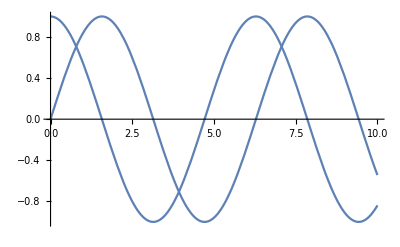

```mathematica
Show[plot1,plot2]
```

Things to observe: 

1. To plot two (or more) functions together, the easiest way is usually to group the functions with braces and use them together as the first argument of the Plot command.

2. You can give names to ANY output of Mathematica commands, not just numerical outputs. Notice how I named the two plots “plot1” and “plot2”. 

3. The Show command can be useful to merge plots together. Notice because it was merging plots together rather than creating a new plot with two functions, it didn’t plot the functions with two separate colors as the first combined plot did. It’s very helpful if you want to combine two different types of plots, like a plot of data points combined with a regular plot like those above (more on that in a later lab).

### How to integrate a function

The ability to perform symbolic computations, such as integrating a function, is a large part of what makes Mathematica so useful. Rare is the physics professor who will make you perform integrals by hand any more.

How to integrate a function symbolically:

```mathematica
f[x_] = - x^4 + 3 x^3 +  4 Sin[x]; (* in case you didn't define it above *)
Integrate[f[x],x]
```

(3 x^4)/4-x^5/5-4 Cos[x]

```mathematica
Integrate[(Sin[x])^2,x]
```

x/2-1/4 Sin[2 x]

```mathematica
Integrate[f[x],{x,y,3 y}]
```

60 y^4-(242 y^5)/5+8 Sin[y] Sin[2 y]

Things to observe: 

1. The second argument of the Integrate command ("x" vs "{x,y,3y}", in the examples above) specifies whether you want an indefinite or a definite integral, and (if the latter) what the limits of integration are.

2. You can either type the function itself into the Integrate command or, if the function has been user-defined, call the defined function (f[x] in this case). Or any sort of mixture of the two.

How to integrate a function numerically:

```mathematica
f[x_] = - x^4 + 3 x^3 +  4 Sin[x]; (* In case you didn't define this function above, I've repeated this command here. The semicolon supresses the output of the command *)Integrate[f[x],{x,0,Pi}]
```

8+(3 π^4)/4-π^5/5

```mathematica
N[%,50]
```

19.852881318445537274781987507841712141235547928899

```mathematica
NIntegrate[f[x],{x,0,Pi}]
```

19.8529

```mathematica
N[%,50]
```

19.8529

```mathematica
Integrate[E^(-Sin[x]^2),{x,-1,1}]
```

∫_-1^1 ⅇ^(-Sin[x]^2)ⅆx

```mathematica
NIntegrate[E^(-Sin[x]^2),{x,-1,1}]
```

1.55964

```mathematica
NIntegrate[E^(-Sin[x]^2),{x,-1,1},WorkingPrecision->50]
```

1.55964039864383999836468987066823398340758217785

```mathematica
Integrate[E^(-x^2),{x,-Infinity,Infinity}]
```

√π

Things to observe: 

1. Both the Integrate and the NIntegrate commands can be used to numerically evaluate an integral. The differences are subtle: the first command first symbolically integrates the function, then plugs in the numbers afterwards. The second command does a numerical integration from the get-go, and can only handle definite integrals. Typically the first one is more useful because it will give you an exact answer if it can give you an answer at all. That’s why the first N[%,50] was able to display fifty decimal places but the second one was not. But sometimes Integrate fails, as in the “E^(-Sin[x]^2)” example, in which case NIntegrate will be the way to go. And if you need more precision than the default setting of NIntegrate, there are options such as WorkingPrecision which can give you that.

2. Mathematica is very sensitive to capitalization. Typing “Nintegrate” will not work at all. If you have any question about how the name of a function should be spelled/capitalized, type your best guess for the name, click on what you just typed, then press F1 to get help.

3. As mentioned above, Infinity is treated as a special constant. It’s often quite useful in integrals.

#### Assignment 1: Position is the integral of velocity

Define a function of time: v(t) = v0 - g t, where v0 is a variable defined to be 5 and g is a variable defined to be 9.8. Define x(t) to be the integral of that function. Plot both v(t) and x(t) on same graph with different colors, for t = 0 to 2.

5

9.8

5-9.8 t

5 t-4.9 t^2

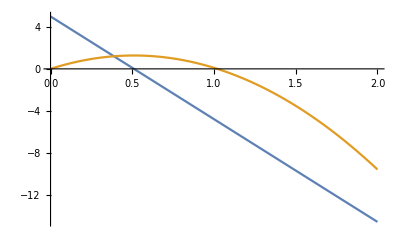

```mathematica
v0 =5
g =9.8
v[t_]=v0-g*t
x[t_]=Integrate[v[t],t]
Plot[{v[t],x[t]},{t,0,2}]
```

### How to differentiate a function

Finding derivatives is another very useful Mathematica feature.

```mathematica
fderiv[x_] =f'[x]
```

f'[x]

```mathematica
fsecondderiv[x_] = f''[x]
```

f''[x]

Things to observe: 

The tick mark  '  tells Mathematica to calculate the derivative. (It’s produced by the apostrophe key.)  Two tick marks gives you a second derivative. The “D” function can also be used for derivatives; see Mathematica’s online help for more details on that.

### How to find when a function equals a specified number

```mathematica
FindRoot[f[x]==-10,{x,-1}]
```

{x→-1.1519}

```mathematica
FindRoot[f[x]==0,{x,3}]
```

{x→3.01795}

Things to observe: 

1. That’s a double equals sign, ==, not a single equals sign, =.  The double equals sign means “test for equality”. In other words, the FindRoot command works by varying x many, many times and testing for equality each time, until it finds the value of x that makes the two sides equal.

2. The FindRoot command actually doesn’t find the roots. It finds when the left side of the double equals sign is equal to the right hand side. If you type in “0” for the right hand side, or if you leave off the right hand side completely, it will indeed find a root of the equation--but in general it is much more flexible than that. This is a very powerful/helpful command!!  Along with making plots and calculating integrals/derivatives, it’s probably the Mathematica command that I personally use the most.

3. The second argument of the FindRoot command, for example “{x,-1}”, specifies where you would like Mathematica to start looking. You can translate the first FindRoot command into English like this: “Find the place around x = -1 where f(x) equals -10.”

Tip: It’s often good to do a plot before you use the FindRoot command, so you can be clever about where you tell Mathematica to start looking.

#### Assignment 2: Solving an equation, numerically

For what value of x (in radians) does cos(x) = x?  
(a) Start by plotting cos(x) and x on the same graph. You can get an approximate answer by looking at where the two curves intersect: that’s where cos(x) equals x. 
(b) Then use FindRoot to get a precise answer.

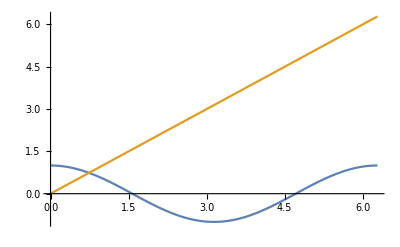

```mathematica
fq[
Plot[{Cos[x],x},{x,0,2Pi}]
```

```mathematica
FindRoot[Cos[x]==x,{x,1}]
```

{x→0.739085}

### How to use the Solve command

```mathematica
Solve[r x == s (3 x - 5), x]
```

{{x→-(5 s)/(r-3 s)}}

```mathematica
Solve[3 x^2 == 4 (3 x - x^2) +5, x]
```

{{x→1/7 (6-√71)},{x→1/7 (6+√71)}}

```mathematica
N[%]
```

{{x→-0.346593},{x→2.06088}}

```mathematica
Solve[ {x + 2 y == 3 , 4 x + 5 y ==6 },{x,y}]
```

{{x→-1,y→2}}

Things to observe:

The Solve command is a lot like FindRoot, and is extremely useful when solving equations. It allows you to do a multitude of tasks: isolate a variable in an algebraic expression, solve a quadratic equation (or any polynomial, I believe), even solve simultaneous equations. Take note of the required syntax; among other things, it uses the "double equals" like FindRoot. Despite its power, however, it also has serious limitations--which is why I myself often turn first to FindRoot if all I want to do is solve numerically for a particular value of x in an equation. On the other hand, FindRoot will only find real numbers, whereas Solve can find complex number solutions.

### How to find the maximum/minimum of a function

There are multiple ways to do this job. Here is one of my favorites:

```mathematica
FindRoot[f'[x]==0,{x,2}]
```

FindRoot::nlnum: The function value {f'[2.]} is not a list of numbers with dimensions {1} at {x} = {2.}.

FindRoot[f'[x]==0,{x,2}]

Things to observe: 

1. I’ve simply combined two functions in one: first the derivative function,  ' , to compute the derivative of the function f, and then the FindRoot command to find where the derivative equals zero. I gave it x=2 as a starting point because I knew from the original plot of f(x) above that x=2 was close to where f(x) had a maximum. Again, making a plot first is often a very useful thing to do.

2. The output of this command just tells you the value of x when f(x) is a maximum. To determine the value of the function itself, you’d have to additionally evaluate f(x) at that value of x.

Here's a built-in command to do the same thing:

```mathematica
FindMaximum[f[x],x]
```

FindMaximum::nrnum: The function value -f[1.] is not a real number at {x} = {1.}.

FindMaximum[f[x],x]

Things to observe: 

1. This command gives you the maximum value of the function in addition to the value of x for which the function has that maximum.

2. There are a tremendous number of built-in functions. This happens to be one that I forgot about for a few years until I rediscovered it. Is it a valuable function? Yes, but since it’s so easy to mimic as I did with FindRoot using the derivative, it’s not nearly as valuable to me as the FindRoot function.  But sometimes it can be worth your while to type a command that you think might exist, then press F1 to see if it shows up in the help file.

#### Assignment 3: Diffraction from a slit

In Physics 232 you hopefully learned that the diffraction pattern produced by a single slit of non-negligible width is given by:  I(x) = I_0  ((sin(πxa/λL))/(πxa/λL))^2, where a is the slit width, L is the distance to the screen where the pattern is being observed, and x is the position on the screen.  (Disclaimer: this involves a small angle approximation.) Sometimes that equation is written in terms of the "sinc" function, where sinc(x)=(sin(x))/x. (Incidentally, Sinc is a pre-defined function in Mathematica, just like Sin itself.) In the equation, I_0 is the intensity at x = 0, i.e. the mid-point of the diffraction pattern; let's just define that as 1 for simplicity.
(a) Make a plot of this function for 3 or 4 maxima around each side of the central maximum, for a 100 micron slit, a 633 nm laser, and a distance to screen = 10 m. Make two plots, actually: one with the default y-axis (meaning intensity)  range, and a second one where you use a PlotRange option to “zoom out” and fully see the central peak.
(b) Determine the position of the first maximum to the right of the central maximum. Side note: In Physics 232 you learned a simple formula for the minima, but there is no similar simple formula for the maxima. They are only approximately located equidistant between the minima.

1/10000

633/1000000000

10

1

(400689 Sin[(10000 π x)/633]^2)/(100000000 π^2 x^2)

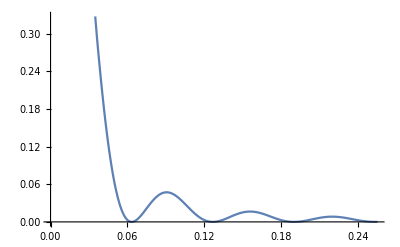

```mathematica
a=100*10^-6 (* slit width converted to meters*)
lambda = 633*10^-9 (* wavelength of laser light converted to meters*)
capL = 10 (*distance from slit to screen in meters*)
capInaught = 1 (*intensity at midpoint of diffraction pattern*)
i[x_]=capInaught*((Sin[(Pi*x*a)/(lambda*capL)]/((Pi*x*a)/(lambda*capL))))^2
Plot[i[x],{x,0,0.255}]
```

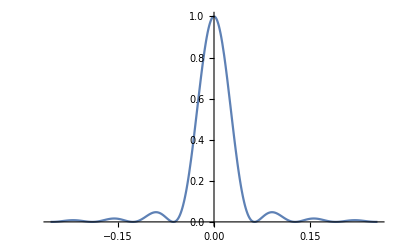

```mathematica
Plot[i[x],{x,-0.255,0.255},PlotRange->All]
```

### How to perform a summation

```mathematica
Sum[1/n^2, {n,1,100}]
```

1589508694133037873112297928517553859702383498543709859889432834803818131090369901/972186144434381030589657976672623144161975583995746241782720354705517986165248000

```mathematica
N[%, 20]
```

1.6349839001848928651

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

```mathematica
N[%]
```

1.64493

```mathematica
Sum[ n x^n, {n,1,10}]
```

x+2 x^2+3 x^3+4 x^4+5 x^5+6 x^6+7 x^7+8 x^8+9 x^9+10 x^10

```mathematica
exptaylor[x_] = Sum[ x^n /n! , {n,0,1000}];
exptaylor[1.2]
```

General::munfl: (1.03533×10^14)/(35028850546302858099329632808581946958330777310287381335557392498211882659489182680375113878«139»57048421341653372149720729437766809178439438827520000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

3.32012

```mathematica
E^1.2
```

3.32012

Things to observe:

1. The Sum command can be very useful to quickly compute numerical summations. The first summation above would be read as “Sum 1/n^2, with n ranging from 1 to 100”. The second argument (which must be in braces) indicates the variable to sum over as well as the summation range, just as in the Integrate command.

2. Sum can be used to determine the value of an infinite summation.

3. Sum can also be used to define functions which include symbolic summations, and in function definitions. I’ve defined exptaylor[x_] to be the sum of the first 1000 terms of the Taylor series for e^x.

4. As mentioned above, a semicolon can be used at the end of a command to suppress the output. Try the exptaylor[x_] function definition command without the semicolon.

5. As you might expect, the “!” symbol can be used to do factorials.

#### *Assignment 4: Two summations

(a) Calculate the value of  ∑_(n=1)^∞ 1/n^6, in both symbolic and numerical form. 
(b) Calculate the value of 1 - 1/2 + 1/3 - 1/4 + 1/5 - 1/6 + ...

```mathematica
Sum[1/(n^6),{n,1,Infinity}]
```

π^6/945

```mathematica
N[%]
```

1.01734

```mathematica
Sum[((-1)^n)/n!,{n,0,Infinity}]
```

1/ⅇ

### How to simplify results

```mathematica
Simplify[1+4 x+6 x^2+4 x^3+x^4]
```

(1+x)^4

```mathematica
complicatedexpression =1/(3 (1+x))-(-1 + 2x)/(6 (1-x +x^2))+2/(3(1 + (1/3) (-1 +2 x)^2))
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

```mathematica
Simplify[complicatedexpression]
```

1/(1+x^3)

```mathematica
complicatedexpression[2]
```

(1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2)))[2]

Things to observe:
  
1. A lot of time symbolic integration or differentiation will give output that looks like the complicated function above. I've gotten into the habit of typing "Simplify[%]" whenever I obtain some output that looks at all like it might be simplifyable.

2. You don’t always have to define a function using the bracket & underscore notation. However, if you don’t you have to be really careful because the results might not be what you expect. In the example above, it might look like I have defined “complicatedexpression” as a function of x. However, what I have actually done is defined “complicatedexpression” as a variable whose value is equal to the three terms involving x. That’s fine here, since I was using the term “complicatedexpression” strictly in place of where I would have to type the expression itself. But if you try typing, for example, “complicatedexpression[2]” to evaluate the function at x=2, Mathematica won’t know what to do. There are ways to treat expressions like that as functions; we’ll get into that in the next lab.

### A bit more algebra

Mathematica has many advanced algebraic functions. “Solve” and “Simplify” are two examples; here are a few more examples of algebraic-related functions that can be helpful. Figure out what each one is doing.

```mathematica
Expand[(1+x)^4]
```

1+4 x+6 x^2+4 x^3+x^4

```mathematica
Together[1/x+1/y]
```

(x+y)/(x y)

```mathematica
Apart[(x+y)/(xy)]
```

x/xy+y/xy

```mathematica
longexpression = 1+4 r+6 r^2+4 r^3+r^4+4 s+12 r s+12 r^2 s+4 r^3 s+6 s^2+12 r s^2+6 r^2 s^2+4 s^3+4 r s^3+s^4
```

1+4 r+6 r^2+4 r^3+r^4+4 s+12 r s+12 r^2 s+4 r^3 s+6 s^2+12 r s^2+6 r^2 s^2+4 s^3+4 r s^3+s^4

```mathematica
Collect[longexpression,s]
```

1+4 r+6 r^2+4 r^3+r^4+(4+12 r+12 r^2+4 r^3) s+(6+12 r+6 r^2) s^2+(4+4 r) s^3+s^4

```mathematica
Collect[longexpression,s, Simplify]
```

(1+r)^4+4 (1+r)^3 s+6 (1+r)^2 s^2+4 (1+r) s^3+s^4

Things to observe:

Collect is one of the subtlest functions of that bunch. It attempts to group the expression in powers of the specified variable. The “Simplify” option is a nice/helpful touch.

## *Cosmetics

Here are various ways you can clean up the look of your notebooks. You don’t have to try them all out, but do look them over so that when the need arises you can say to yourself, “Wasn’t there something about this in Lab1?”

### How to make input cells look pretty

I personally prefer to type equations/expressions exactly the way you’ve seen in this notebook so far, typing them out using function names/parentheses/etc. However, some prefer using the math input “palette” to help you type them in. You can open that palette via Palettes→Basic Math Assistant. Explore the options there if you’d like.That palette has a host of formatting capabilities. One of those is the ability to add Greek letters (they are under “Typesetting”)--but if that’s all you need, my own preference to get Greek letters is via the Insert→Special Character menu item. Or even better, type Esc, then the name of the letter, then Esc again. 
EsclambdaEsc 

You can also accomplish many formatting tasks using keyboard shortcuts. See for example the documentation on Two-Dimensional Input and Special Characters.

```mathematica
Esc Lambda Esc
```

Esc^2 Lambda

### Changing the “style” of a cell

The most helpful thing under the Format menu is setting the style of a cell, under Format → Style → < various styles > . That allows you to change a cell to Text style, for example, so that it won' t be evaluated as input, or to create section titles, bullet points, and so forth. Try changing this cell to a different style to see what happens, resetting it to "Text" when you are done. Be sure to select the whole cell as you do this by first clicking on the relevant vertical bar on the right.

### Changing the appearance of the whole notebook

The Format→Stylesheet submenu changes the look and feel of the whole notebook by altering the fonts and colors associated with each style.  The stylesheet used here is the Report→StandardReport stylesheet. Try changing this just for fun. You can edit existing stylesheets or even create new ones.

Also, Control-Mousewheel is a nice trick for making the text of the whole document get bigger or smaller, just as in most web browsers.

### Changing the appearance of individual words

As in most word processors, Control-B and Control-I produce bolded and/or italicized text.  The Format menu options can also be used to alter the font/face/size/color of a specific word or phrase, though I myself don’t often bother with that capability.

### Splitting/merging cells

The Cell→Divide Cell and Cell→Merge Cells options can sometimes be quite useful.  In the input cell below, place your cursor at the beginning of the second expression and split the cell into two separate cells.  Then select both cells and merge them back together again.  When the cells split or merge, notice that the cell brackets at the right also split and merge.

```mathematica
1+1
2/2
```

### How to “clean up” output cells

The Cell→Delete All Output option deletes every output cell in the entire notebook.  This can be useful when cleaning up your notebook at the end of a session, but it can't be undone (although, as mentioned above, you can do a Control-A followed by shift-enter to reevaluate everything from scratch).

## Additional Assignments

Solve the following problems. If you get stuck, you can ask me or a nearby student for help.

#### *Assignment 5: The plot thickens

Make a plot of x^4 + 2 x^3 +3 x^2+ 4 x+5, from x = -3 to x = 3. Experiment with different plot styles as options, such as PlotStyle→Thick,  or PlotStyle→Red (or Blue, or Green, or Magenta, etc.), or PlotStyle→Dashed  (or Dotted, or DotDashed), or PlotStyle→Opacity[0.5] (or Opacity[0.1], or Opacity[0.8], etc.). After you have experimented a bit with these options, choose your favorite plot styles and combine them together via a list enclosed in braces: PlotStyle→{option1, option2, option3, etc.}.

5+4 x+3 x^2+2 x^3+x^4

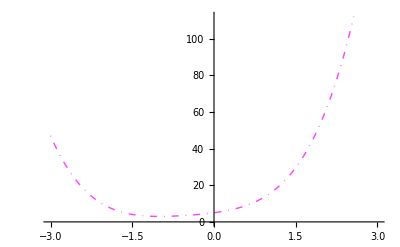

```mathematica
q[x] = x^4+2x^3+3x^2+4x+5
Plot[q[x],{x,-3,3},PlotStyle->{DotDashed,Opacity[0.75],Magenta,Thick}]
```

#### *Assignment 6: Polynomial roots

As you should have just seen from the plot, the polynomial x^4 + 2 x^3 + 3 x^2 + 4 x + 5 has no real roots. (It doesn' t cross zero anywhere.) It does, however, have four complex roots. What are they? Find them in decimal form.

```mathematica
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,-1*I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,(1/2)*I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,(-1/2)*I}]
```

{x→0.287815+1.41609 ⅈ}

{x→0.287815-1.41609 ⅈ}

{x→-1.28782+0.857897 ⅈ}

{x→-1.28782-0.857897 ⅈ}

{x→0.287815-1.41609 ⅈ}

```mathematica
NSolve[Reduce[q[x]*I==0],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→q^(-1)[0.]}}

```mathematica
Reduce[%]
```

Reduce::naqs: {x→q^(-1)[0.]} is not a quantified system of equations and inequalities.

Reduce[{{x→q^(-1)[0.]}}]

#### *Assignment 7: Taylor’s series of e^x

The Taylor’s series of e^x evaluated at x = 1 is 1 + 1 + 1/2 + 1/3! + 1/4!  + ... .  Show that this series gets closer and closer to the true value of e  (=e^1) as you include more and more terms. Try 5 terms (as shown), 10 terms, and 100 terms; give your results to 50 decimal places. Also display e to 50 decimal places for comparison.

```mathematica
N[E,50]
N[1+1+(1/2)+(1/(3!))+(1/(4!)), 50]
N[Sum[1/(n!),{n,0,5}],50]
N[Sum[1/(n!),{n,0,10}],50]
N[Sum[1/(n!),{n,0,100}],50]
N[E,50]
```

2.7182818284590452353602874713526624977572470937

2.7083333333333333333333333333333333333333333333333

2.7166666666666666666666666666666666666666666666667

2.7182818011463844797178130511463844797178130511464

2.7182818284590452353602874713526624977572470937

2.7182818284590452353602874713526624977572470937

#### *Assignment 8: A basic derivative

Define the function f8(x) = (sin^2(x))/(1+cos(x)). Take its derivative, and simplify the result.

```mathematica
f8[x_]=Sin[x]^2/(1+Cos[x])
f8'[x]
Simplify[f8'[x]]
```

Sin[x]^2/(1+Cos[x])

(2 Cos[x] Sin[x])/(1+Cos[x])+Sin[x]^3/(1+Cos[x])^2

Sin[x]

#### *Assignment 9: A basic integral

Determine  ∫e^-x sin(x)ⅆx, integrated from 0 to infinity.

```mathematica
f9[x_]=Sin[x]*E^(-x)
Integrate[f9[x],{x,0,Infinity}]
```

ⅇ^-x Sin[x]

1/2

#### Complex Numbers & Functions of Complex Numbers

Let’s start with a simple complex number in z = x + iy format (rectangular format):

```mathematica
z=4+3I
```

It has real and imaginary parts:

```mathematica
Re[z]
Im[z]
```

And we can calculate its complex conjugate:

```mathematica
Conjugate[z]
```

When plotted on the complex plane (x-axis is the real axis, y-axis is the imaginary axis), then the length (the absolute value, or magnitude of z) and angle of that line provides us with the parameters for representing z in polar format:

```mathematica
Abs[z]
Arg[z]
```

You can do many of these things quite simply using the “suggestions bar” that appears when you evaluate an input or click on an output box.  Try that by executing the input line below, and choose “convert to exponential” to convert the rectangular format of z to a polar format.  When you do this you’ll recognize in this format the absolute value and the angle that you calculated above.

```mathematica
z
```

This is essentially Euler’s equation: z = e^iθ = cos(θ) + i sin(θ) = x + iy. 
Now instead of working with an individual complex number, let’s think about a simple complex function written in polar format,  z = e^ix:

```mathematica
f[x_]= E^(I x)
```

The real part should be cos(x).  Let’s see:

```mathematica
Re[f[x]]
```

Well this is certainly true, but not particularly helpful.  The suggestions bar offers the suggestion “FullSimplify”.  Give that a try:

```mathematica
FullSimplify[Re[ⅇ^(ⅈ x)]]
```

Still no cosine function.  However, as you’ll see next, it seems Mathematica can still evauate Re(f(x)) at a point, and has no trouble plotting it as a function of x:

```mathematica
Re[f[Pi/4]]
Plot[Re[f[x]],{x,0,15}]
```

What’s happeining here?  The problem is that Mathematica doesn’t know in general whether x is real, imaginary or complex. When we ask it to evaluate f(x) for a real value of x, or plot f(x) over a range of real values then we’re making it explicit that we’re talking about real values of x.  But Mathematica can’t know if that is always the case.  This is a perfect example of a situation where we need to provide Mathematica with a little more information.   Let’s declare x to be a real number.  Here’s what that looks like:

```mathematica
$Assumptions=x∈Reals
```

```mathematica
Re[f[x]]
```

```mathematica
FullSimplify[Re[ⅇ^(ⅈ x)]]
```

The Assumptions statement says “x is an element of the set of real numbers”.  The symbol ∈, “is an element of,” is produced by typing the sequence Esc elem Esc.
The power of the FullSimplify command is that it takes any assumptions that have been made and applies them in making the simplification.

#### *Assignment 10: A basic complex number calculation

(a) Calculate the magnitude and angle (in radians) of:  (4 + 5i) ÷ (6 - 7i).  Give your answers in decimal form to 8 sig figs.
(b) Show that the magnitude squared of the number is also the number times its complex conjugate

```mathematica
a10=(4+5I)/(6-7I)
```

-11/85+(58 ⅈ)/85

Plot::plld: Endpoints for Charting`Private`pvar$9152 in {Charting`Private`pvar$9152,0,0} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[a10,{x,0,ⅈ}]

```mathematica
re =Re[(a10)]
im =Im[a10]
mag =Sqrt[re^2+im^2](*calculates magnitude of a10*)
ang =N[ mag*Tan[im/re]]
```

-11/85

58/85

√(41/85)

1.10694

#### Assignment 11: Superposition of wavefunctions

Define two wavefunctions: ψ1 = e^(i k1 x) and ψ2 = e^(i k2x), where k1 = 1 and k2 = 2.  (If you want, you can get the Greek letter ψ by typing Esc psi Esc.  Or just call it psi!)  
(a) Plot the real parts of ψ1 and ψ2 on the same graph using different colors, over the x-range 0 to 15.  Then on a second graph and over the same range, plot the real part of the superposition ψ12 = ψ1 + ψ2.
(b) Define the (non-normalized) probability function prob1 to be the wavefunction ψ1 times its complex conjugate.  Do the same for prob2 and prob12.
(c) Show that even though the wavefunctions are complex, the probabilities are always real.  Hint: use $Assumptions and FullSimplify, or play around with the commands ExpToTrig or ComplexExpand (which makes its own assumptions) in combination with Simplify.
(b) Make a plot of the probabilities which demonstrates that prob12 ≠ prob1 + prob2.

```mathematica
(*setup*)
k1 = 1
k2 = 2
ψ1[x_]=E^(I*k1*x)
ψ2[x_]=E^(I*k2*x)
ψ12[x_]=ψ1[x]+ψ2[x]
```

1

2

ⅇ^(ⅈ x)

ⅇ^(2 ⅈ x)

ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)

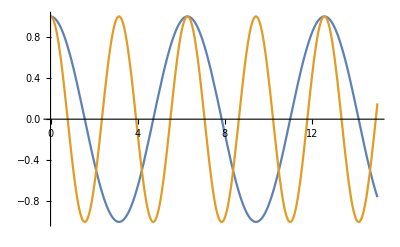

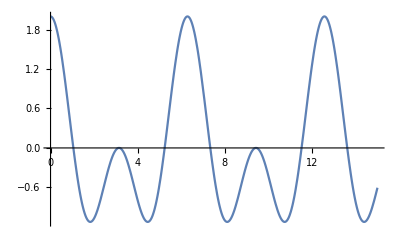

```mathematica
(*a*)
Plot[{Re[ψ1[x]],Re[ψ2[x]]},{x,0,15}]
Plot[Re[ψ12[x]],{x,0,15}]
```

```mathematica
(*b*)
prob1[x_]=ψ1[x]*Conjugate[ψ1[x]]
prob2[x_]=ψ2[x]*Conjugate[ψ2[x]]
prob12[x_]=ψ12[x]*Conjugate[ψ12[x]]
```

ⅇ^(ⅈ x-ⅈ Conjugate[x])

ⅇ^(2 ⅈ x-2 ⅈ Conjugate[x])

(ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)) (ⅇ^(-ⅈ Conjugate[x])+ⅇ^(-2 ⅈ Conjugate[x]))

```mathematica
(*c*)
ComplexExpand[ψ1[x]]
ComplexExpand[prob1[x]]
ComplexExpand[ψ2[x]]
ComplexExpand[prob2[x]]
ComplexExpand[ψ12[x]]
ComplexExpand[prob12[x]]
```

Cos[x]+ⅈ Sin[x]

1

Cos[2 x]+ⅈ Sin[2 x]

1

Cos[x]+Cos[2 x]+ⅈ (Sin[x]+Sin[2 x])

Cos[x]^2+2 Cos[x] Cos[2 x]+Cos[2 x]^2+Sin[x]^2+2 Sin[x] Sin[2 x]+Sin[2 x]^2

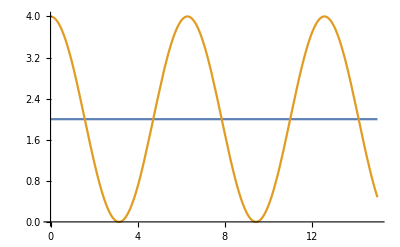

```mathematica
(*d*)
Plot[{prob1[x]+prob2[x],prob12[x]},{x,0,15}]
```

## A glimpse behind the curtain

### Functions that are behind the shorthand

All Mathematica expressions down to something as simple as “2 + 2” can be written as function calls. Here is what Mathematica really is “thinking” when you type in some simple things.

```mathematica
3+4+5  
Plus[3,4,5]
```

```mathematica
x y z
Times[x,y,z]
```

```mathematica
x^2
Power[x,2]
```

```mathematica
q=4
Set[q,4]
```

### What Mathematica actually "sees"

Mathematica not only interprets shorthand notation as functions, it actually interprets nearly everything as functions. Cell→Show Expression shows you how Mathematica  views a cell. Try it on this very simple text cell, for example. This feature can be toggled on and off -- so don't panic and accidentally delete the whole cell to escape the garbage on the screen!

## Wrap-up

Click on any of the terms in blue to bring up the help file for more information.

The following functions were discussed in this worksheet, or are very closely related:
Operators:  +, -, *, /, ^, !
Basic Functions: Log, Log10, Sqrt
Trig Functions: Sin, Cos, Tan, ArcSin, ArcCos, ArcTan, Sinc
Forcing numerical output: N
Referring to previous results: %, %% (and so on), %[number]  (all related to Out function)
Built-in constants: Pi, E, I, Infinity
Functions: f[x_] notation to define your own function, f[x] to refer to the function, Plot (and PlotRange option) to display the function
Calculus-related functions: Integrate, NIntegrate, derivatives via ‘, ‘’ (and so on)  (all related to D function)
Misc: FindRoot, FindMaximum, FindMinimum, Sum, Solve
Complex Numbers: Abs,  Arg, Re, Im, Conjugate , FullSimplify, ExpToTrig, TrigToExp
Assumptions: $Assumptions

Potentially useful summary/tutorial pages:
Operators
Some mathematical functions 
Mathematical Constants 
Defining functions
Solving Equations
Comments (*  *)
Complex numbers tutorial

## What to turn in

When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#2-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 11).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.

Here’s what it should look like: